```mathematica
Integrate[t^λ/(2 Pi l Sqrt[2])Exp[- t y^2/(2Pi l^2)],{t,0,Infinity}]
```

ConditionalExpression[(2^(-1/2+λ) π^λ (y^2/l^2)^(-1-λ) Gamma[1+λ])/l,Re[y^2/l^2]>0&&Re[λ]>-1]

```mathematica
(2^(-1/2+λ) π^λ (y^2/l^2)^(-1-λ) Gamma[1+λ])/l/.λ->-3/2
```

-(√(y^2/l^2))/(2 l π)

```mathematica
L^3/(2Pi l)^4 Integrate[t^(9/2)/t^3 Exp[- t y^2/(2Pi l^2)],{t,0,Infinity}]
```

ConditionalExpression[(3 L^3)/(8 √2 l^4 π (y^2/l^2)^(5/2)),Re[y^2/l^2]>0]

```mathematica
Eigensystem[e({{0, 1}, {1, 0}})]
```

{{-e,e},{{-1,1},{1,1}}}

```mathematica
(1+λ)Exp[-I Pi n]-(1-λ) (1+λ)/(1-λ)Exp[I Pi n]/.n->2
```

0

```mathematica
Solve[(1+λ)Exp[-I Pi n]-(1-λ) (1+λ)/(1-λ)Exp[I Pi n]==0,n]
```

{{n→ConditionalExpression[-2 C[1],C[1]∈ℤ]},{n→ConditionalExpression[(ⅈ (ⅈ π+2 ⅈ π C[1]))/π,C[1]∈ℤ]}}

```mathematica
Solve[(1+λ)Exp[-I Pi n]+(-1+λ)Exp[I Pi n]==0,n]
```

{{n→ConditionalExpression[(ⅈ (2 ⅈ π C[1]+Log[-(√(1-λ))/(√(1+λ))]))/π,C[1]∈ℤ]},{n→ConditionalExpression[(ⅈ (2 ⅈ π C[1]+Log[(√(1-λ))/(√(1+λ))]))/π,C[1]∈ℤ]}}

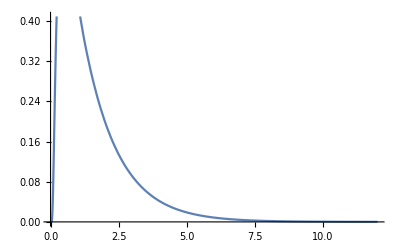

```mathematica
Plot[EllipticTheta[1,0.5,Exp[- Pi t]],{t,0,12}]
```

```mathematica
Solve[F/Sqrt[1-F^2]==g m,F]
```

{{F→-(g m)/(√(1+g^2 m^2))},{F→(g m)/(√(1+g^2 m^2))}}

```mathematica
1/Sqrt[1-F^2]/.%
```

```mathematica
Eigensystem[({{x, y}, {-y, x}})]//Simplify
```

{{x-ⅈ y,x+ⅈ y},{{ⅈ,1},{-ⅈ,1}}}

```mathematica
M=({{1, -2 Pi l^2 e}, {2 Pi l^2 e, 1+Dϕ^2}})/.e->Dϕ;
Inverse[M]//Simplify
```

{{(1+Dϕ^2)/(1+Dϕ^2+4 Dϕ^2 l^4 π^2),(2 Dϕ l^2 π)/(1+Dϕ^2+4 Dϕ^2 l^4 π^2)},{-(2 Dϕ l^2 π)/(1+Dϕ^2+4 Dϕ^2 l^4 π^2),1/(1+Dϕ^2 (1+4 l^4 π^2))}}

```mathematica
I Log[(√(1-λ))/(√(1+λ))/.λ-> Tan[I x]]//FullSimplify
```

ArcTan[Tanh[x]]

```mathematica
Eigensystem[({{(1+e^2)/(1-e^2), (2e)/(1-e^2)}, {(2e)/(1-e^2), (1+e^2)/(1-e^2)}})]//Simplify
```

{{(1+e)/(1-e),(1-e)/(1+e)},{{1,1},{-1,1}}}

```mathematica
2 Pi l^2 Integrate[(t^(9/2) t^(-3/2))/(t (2t)^(4/2))Exp[- t y^2/2Pi l^2],{t,0,Infinity}]
```

ConditionalExpression[1/y^2,Re[l^2 y^2]>0]

```mathematica
(2^(-1/2+λ) π^(-2-λ) (l^2 y^2)^(-1-λ))/l^2/.λ->(-6/2)
```

(l^2 π y^4)/(8 √2)

```mathematica
Series[DedekindEta[I t]^9,{t,0,1}]
```

ⅇ^(-(3 π)/(4 t)+O[t]^6) (1/t^(9/2)+O[t]^(3/2))

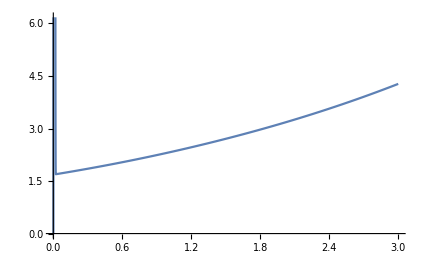

```mathematica
Plot[Abs[Exp[Pi/(4t)] Sqrt[t] EllipticTheta[1,I t,Exp[-Pi t]]],{t,0,3}]
```

```mathematica
Series[1/(Sqrt[2 t] t)EllipticTheta[1,I θ t/2,Exp[-Pi t]]^4/(EllipticTheta[1,I θ t,Exp[-Pi t]] DedekindEta[I t]^9),{t,0,3}]
```

ⅇ^((3 π)/(4 t)+O[t]^6) ((EllipticTheta[1,0,1]^3 t^3)/(√2)+O[t]^4)

```mathematica
Series[ EllipticTheta[1,I θ t/2,Exp[-Pi t]]^3/EllipticTheta[1,I θ t,Exp[-Pi t]],{t,0,0}]
```

EllipticTheta[1,0,1]^2+O[t]^1

```mathematica
Series[EllipticTheta[1,I θ t,Exp[-Pi t]],{θ,0,1}]
```

ⅈ t EllipticThetaPrime[1,0,ⅇ^(-π t)] θ+O[θ]^2

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::munfl: (4.3375×10^-201+0. ⅈ) (4.3375×10^-201+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

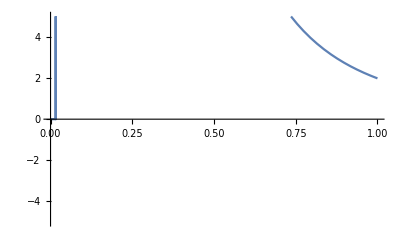

```mathematica
Plot[Abs[(EllipticTheta[1,I t/2,Exp[-Pi t]]^4/(DedekindEta[I t]^9 EllipticTheta[1,I t,Exp[-Pi t]]))^-1],{t,0,1},PlotRange->5]
```